# Homework 6

## By Marvyn Bailly

## Question 1

Consider the equation and boundary conditions

```mathematica
ClearAll["Global`*"]
eqn=ϵ*D[y[x],{x,2}] + b[x]*D[y[x],{x,1}] + c[x]*y[x]
BC1 = y[0] - A
BC2 = y[l] - B
```

c[x] y[x]+b[x] y'[x]+ϵ y''[x]

-A+y[0]

-B+y[l]

where b(x), c(x), l, A, and B are

```mathematica
b[x_] = (1 + x)^2;
c[x_] = 1;
l = 1;
A = 1;
B = 1;
```

Thus the problem is

```mathematica
eqn
BC1
BC2
```

y[x]+(1+x)^2 y'[x]+ϵ y''[x]

-1+y[0]

-1+y[1]

The WKB expansion takes the form

```mathematica
y[x_] = Exp[(S0[x] + ϵ*S1[x] + ϵ^2*S2[x])/ϵ]
```

ⅇ^((S0[x]+ϵ S1[x]+ϵ^2 S2[x])/ϵ)

Plugging this into our equation yields

```mathematica
eqn
BC1
BC2
```

ⅇ^((S0[x]+ϵ S1[x]+ϵ^2 S2[x])/ϵ)+(ⅇ^((S0[x]+ϵ S1[x]+ϵ^2 S2[x])/ϵ) (1+x)^2 (S0'[x]+ϵ S1'[x]+ϵ^2 S2'[x]))/ϵ+ϵ ((ⅇ^((S0[x]+ϵ S1[x]+ϵ^2 S2[x])/ϵ) (S0'[x]+ϵ S1'[x]+ϵ^2 S2'[x])^2)/ϵ^2+(ⅇ^((S0[x]+ϵ S1[x]+ϵ^2 S2[x])/ϵ) (S0''[x]+ϵ S1''[x]+ϵ^2 S2''[x]))/ϵ)

-1+ⅇ^((S0[0]+ϵ S1[0]+ϵ^2 S2[0])/ϵ)

-1+ⅇ^((S0[1]+ϵ S1[1]+ϵ^2 S2[1])/ϵ)

Now we collect the O(1/ϵ) and O(1) terms (dividing out exp term)

```mathematica
Clear[leadSol,S0]
leadSol[x_] = Coefficient[eqn,ϵ,-1] /. ⅇ^((S0[x]+ϵ S1[x]+ϵ^2 S2[x])/ϵ) -> 1
nextSol[x_] = Coefficient[eqn,ϵ,0] /. ⅇ^((S0[x]+ϵ S1[x]+ϵ^2 S2[x])/ϵ) -> 1
```

S0'[x]+2 x S0'[x]+x^2 S0'[x]+S0'[x]^2

1+S1'[x]+2 x S1'[x]+x^2 S1'[x]+2 S0'[x] S1'[x]+S0''[x]

Notice that the leading order problem

```mathematica
FullSimplify[leadSol[x]]
```

S0'[x] ((1+x)^2+S0'[x])

Thus there are two cases, when S_(0_x)=0 or S_(0_x)=-b(x)

#### Case 1

In the case that S_(0_x)=0 (the outer problem):

```mathematica
Clear[S0]
DSolve[S0'[x]==0,S0[x],x] /. {C[1] -> c1,C[2] -> c2}
S0[x] = S0[x] /. %[[1]]
```

{{S0[x]→c1}}

c1

Thus the O(1) term becomes

```mathematica
nextSol1[x_] = nextSol[x] /. {S0'[x] -> 0,S0''[x] -> 0}
```

1+S1'[x]+2 x S1'[x]+x^2 S1'[x]

Now we solve for S_1

```mathematica
t = DSolve[nextSol1[x]==0,S1[x],x][[1]][[1]][[2]]
FullSimplify[Exp[(S0[x] + ϵ*t)/ϵ]] /. c1 -> 0
```

1/(1+x)+C[1]

ⅇ^(1/(1+x)+C[1])

#### Case 2

In the case when S_(0_x)=-b(x)

```mathematica
Clear[S0]
S0[x] = Integrate[-b[x],x]
S0'[x] = D[S0[x],x]
S0''[x] = D[S0[x],{x,2}]
nextSol2[x_] = FullSimplify[nextSol[x]]
```

-x-x^2-x^3/3

-1-2 x-x^2

-2-2 x

0

Now we solve for S_1

```mathematica
S1[x_] = DSolve[nextSol2[x]==0,S1[x],x][[1]][[1]][[2]]
```

-1/(1+x)+C[1]-2 Log[1+x]

```mathematica
Integrate[1/b[ξ],{ξ,0,x}]
```

ConditionalExpression[x/(1+x), Re[x]>-1||x∉ℝ]

```mathematica
Expand[(1+x)^3/3]
```

1/3+x+x^2+x^3/3

```mathematica
y[x_] = C1 *Exp[1/(1+x)] + C2/(1+x)^2*Exp[1/ϵ(-x - x^2 - x^3/3) - 1/(1+x)]
Solve[{y[x] == C1 *Exp[1/(1+x)] + C2/(1+x)^2*Exp[1/ϵ(-x - x^2 - x^3/3) - 1/(1+x)],y[0] == 1, y[1]==1},{C1,C2}]
```

C1 ⅇ^(1/(1+x))+(C2 ⅇ^(-1/(1+x)+(-x-x^2-x^3/3)/ϵ))/(1+x)^2

{{C1→-(-ⅇ+4 ⅇ^(1/2+7/(3 ϵ)))/(ⅇ (ⅇ-4 ⅇ^(7/3/ϵ))),C2→-(4 (-1+√ⅇ) ⅇ^(1+7/(3 ϵ)))/(-ⅇ+4 ⅇ^(7/3/ϵ))}}

```mathematica
C1=-(-ⅇ+4 ⅇ^(1/2+7/(3 ϵ)))/(ⅇ (ⅇ-4 ⅇ^(7/3/ϵ)))
C2=-(4 (-1+√ⅇ) ⅇ^(1+7/(3 ϵ)))/(-ⅇ+4 ⅇ^(7/3/ϵ))
y[x_,ϵ_] = C1 *Exp[1/(1+x)] + C2/(1+x)^2*Exp[1/ϵ(-x - x^2 - x^3/3) - 1/(1+x)]
```

-(-ⅇ+4 ⅇ^(1/2+7/(3 ϵ)))/(ⅇ (ⅇ-4 ⅇ^(7/3/ϵ)))

-(4 (-1+√ⅇ) ⅇ^(1+7/(3 ϵ)))/(-ⅇ+4 ⅇ^(7/3/ϵ))

-(ⅇ^(-1+1/(1+x)) (-ⅇ+4 ⅇ^(1/2+7/(3 ϵ))))/(ⅇ-4 ⅇ^(7/3/ϵ))-(4 (-1+√ⅇ) ⅇ^(1-1/(1+x)+7/(3 ϵ)+(-x-x^2-x^3/3)/ϵ))/((-ⅇ+4 ⅇ^(7/3/ϵ)) (1+x)^2)

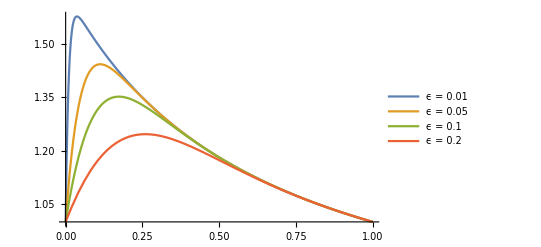

```mathematica
Plot[{y[x,0.01],y[x,0.05],y[x,0.1],y[x,0.2]},{x,0,1},PlotLegends->{"ϵ = 0.01","ϵ = 0.05","ϵ = 0.1","ϵ = 0.2"}]
```